# Math 223: Homework 7

Hardeep Bassi

03/22/2023

## Problem 1

Find the first two terms of the asymptotic expansion of .

As usual, we integrate by parts. Let . This means our integral yields:
. Hence we have found our first two terms

```mathematica
(1/x) * Integrate[Exp[-x*t]/t^2,{t,5,9}]
```

(1/45 ⅇ^(-9 x) (-5+9 ⅇ^(4 x))-x ExpIntegralEi[-9 x]+x ExpIntegralEi[-5 x])/x

```mathematica
Limit[(1/45 ⅇ^(-9 x) (-5+9 ⅇ^(4 x))-x ExpIntegralEi[-9 x]+x ExpIntegralEi[-5 x])/x/(-E^(-9x)/9x + E^(-5x)/5x), x->Infinity ]
```

0

Since the first two terms dominate the remaining integral, we see that

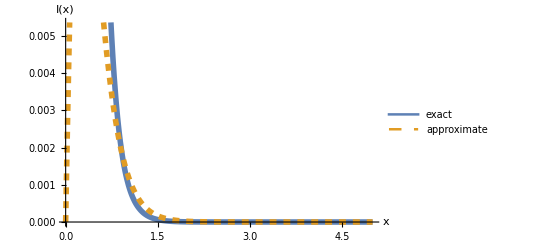

```mathematica
Plot[{ExpIntegralEi[-9 x]-ExpIntegralEi[-5 x], ((-E^(-9x)/9x) + (E^(-5x)/5x))},{x,0,5},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"exact", "approximate"}]
```

## Problem 2

Use Watson’s Lemma to determine the asymptotic expansion of 
First, we see the conditions of Watson’s lemma according to https://en.wikipedia.org/wiki/Watson%27s_lemma are satisfied by taking   and . Hence, we may invoke Watson’s lemma as in lecture. We can expand the non-exponential terms about 0 as:

```mathematica
Collect[Series[(t^(-1/3)Cos[t]), {t,0,2}],t]
```

1/t^(1/3)-t^(5/3)/2

With this, we apply Watson’s lemma as:

```mathematica
Collect[Integrate[ ⅇ^(-x t)*(1/t^(1/3)-t^(5/3)/2), {t, 0, ∞}, Assumptions->x>0],x]
```

-(5 Gamma[2/3])/(9 x^(8/3))+Gamma[2/3]/x^(2/3)

Yielding that  -(5 Gamma[2/3])/(9 x^(8/3))+Gamma[2/3]/x^(2/3). To check the approximation, we can plot as:

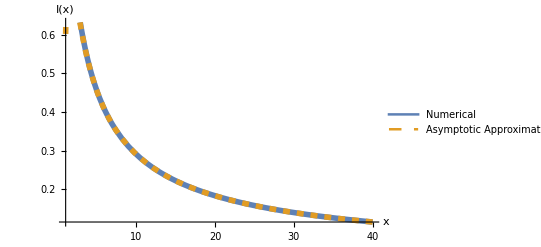

```mathematica
Plot[{NIntegrate[(t)^(-1/3)ⅇ^(-x t)Cos[t],{t,0,Pi}],-(5 Gamma[2/3])/(9 x^(8/3))+Gamma[2/3]/x^(2/3)},{x,1,40},
	PlotStyle-> {Directive[Solid,Thickness[0.01]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Numerical","Asymptotic Approximation"}]
```

## Problem 3

Use Laplace’s method to determine the leading behavior of 
First, we seek our the local minimum of , since we see that our  function is now non-monotonic. By inspection, we see that  has  and our  is smooth alongside . Using this, we can series expand as:

```mathematica
Series[Sin[t]^4,{t,0,6}]
```

t^4-(2 t^6)/3+O[t]^7

This means we have that

```mathematica
Integrate[E^(-x*t^4),{t,-Infinity,Infinity}, Assumptions->x>0]
```

(2 Gamma[5/4])/x^(1/4)

We can check the approximation as:

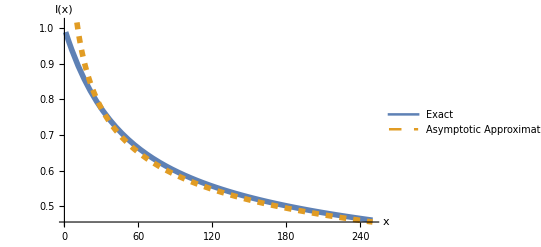

```mathematica
Plot[{NIntegrate[ⅇ^(-x Sin[t]^4),{t,-1/2,1/2}],(2Gamma[5/4])/x^(1/4)},{x,1,250},
PlotStyle-> {Directive[Solid,Thickness[0.01]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact","Asymptotic Approximation"}]
```

This looks good as we go to infinity, which is what we expect.